```mathematica
Simplify[ Cos[ ArcSin[ x ]] ]
```

√(1-x^2)

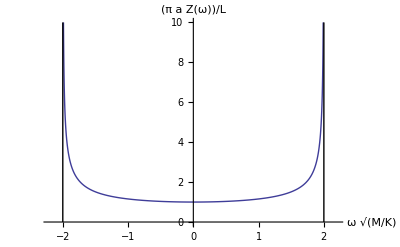

```mathematica
Module[{r, p, h, w, g},
r = 2.2 ;
h = 10 ;
w = 2 ;
p = Plot[ (*ArcSin[Sqrt[x^2/4]]*)1/Sqrt[1 - x^2/4], {x, -w, w} 
, PlotRange -> {{-r, r}, {0, h}} 
, AxesLabel->{Sqrt[M/K] ω, Pi a "Z(ω)"/L}
] ;
g = Graphics[{
Line[{{w, 0}, {w, h}}],
Line[{{-w, 0}, {-w, h}}]
}
] ;
Show[p, g]

]
```

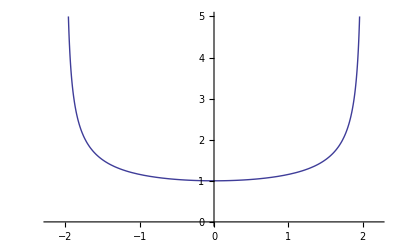
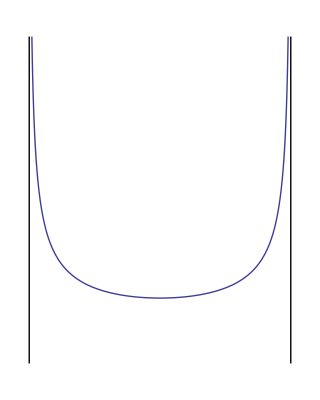

```mathematica
Module[{p,g},p=Plot[1/Sqrt[1-x^2/4],{x,-2,2},PlotRange->{{-2.2,2.2},{0,5}}];
g=Graphics[{Line[{{2,0},{2,5}}],Line[{{-2,0},{-2,5}}]}];
{p, Show[g,p]}]
```

```mathematica
Integrate[ ArcSin[Sqrt[x^2/4]]/Sqrt[1 - x^2/4], {x, -2, 2}] // N
```

4.9348

```mathematica
Integrate[ 1/Sqrt[1 - x^2], {x, -1, 1}]
```

π

```mathematica
Integrate[1/Cos[x], x] // Simplify
```

-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]